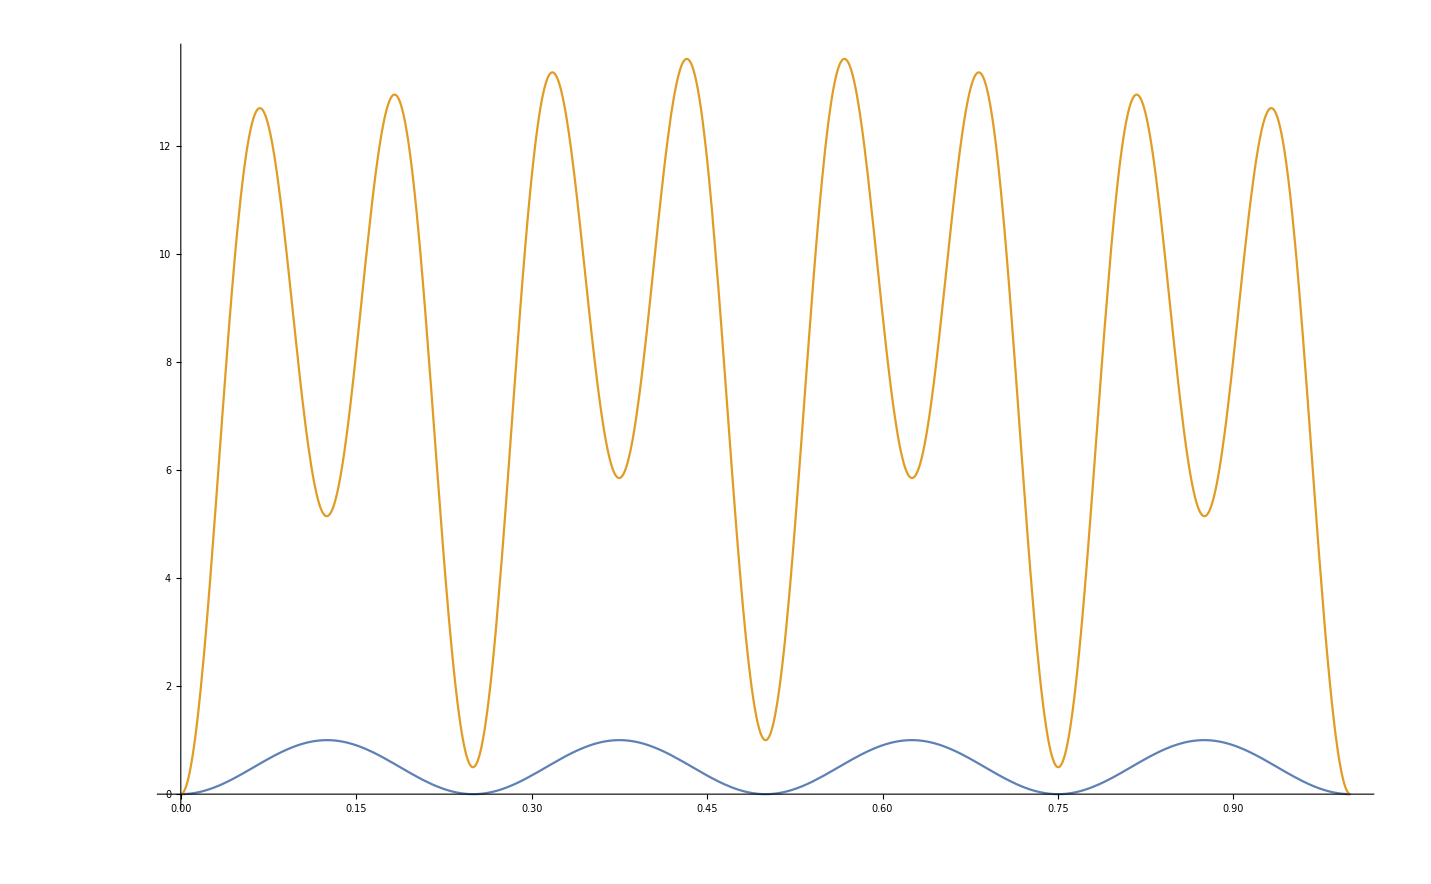

```mathematica
Plot[{Sin[4*π*x]^2,Sin[π x]^2+5*Sin[4π x]^2+10*Sin[8 π x]^2},{x,0,1}]
```

```mathematica
leqn = Laplacian[u[x,y],{x,y}] == 2000*(Sin[4 π x]*Sin[4 π y])^5;
bc1 = u[x,0]==Sin[π x]^2+5Sin[4 π x]+10 Sin[8 π x]^2;
bc2 = u[0,y]==Sin[4 π y]^2;
bc3 = u[x,1]==0;
bc4 = u[1,y]==0;
sol = NDSolve[{leqn,bc1,bc2},u[x,y],{x,y}]
```

NDSolve::underdet: There are more dependent variables, {u[x,0],u[x,y],u^(0,2)[x,y]}, than equations, so the system is underdetermined.

NDSolve[{u^(0,2)[x,y]+u^(2,0)[x,y]==2000 Sin[4 π x]^5 Sin[4 π y]^5,u[x,0]==Sin[π x]^2+5 Sin[4 π x]+10 Sin[8 π x]^2,u[0,y]==Sin[4 π y]^2},u[x,y],{x,y}]

```mathematica
leqn=Laplacian[u[x,y],{x,y}]==2000*(Sin[4 π x]*Sin[4 π y])^5;
bc=u[x,0]==UnitBox[x];
sol=DSolve[{leqn,bc},u[x,y],{x,y}]
```

```mathematica
DSolve[{Derivative[0,2][u][x,y]+Derivative[2,0][u][x,y]==2000 Sin[4 π x]^5 Sin[4 π y]^5,u[x,0]==UnitBox[x]},u,{x,y}]
```

```mathematica
sol=NDSolve[{Laplacian[u[x,y],{x,y}]==2000*(Sin[4 π x]*Sin[4 π y])^5,bc1,bc2,bc3,bc4},u,{x,0,1},{y,0,1}]
```

{{u→InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]}}

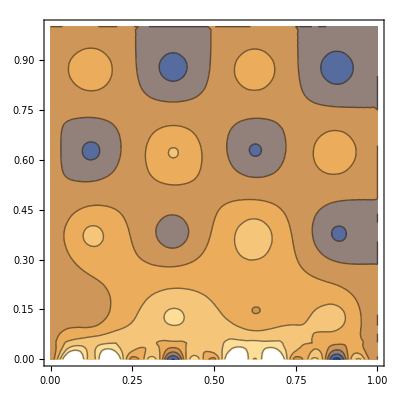

```mathematica
ContourPlot[Evaluate[u[x,y]/.sol],{x,0,1},{y,0,1}]
```

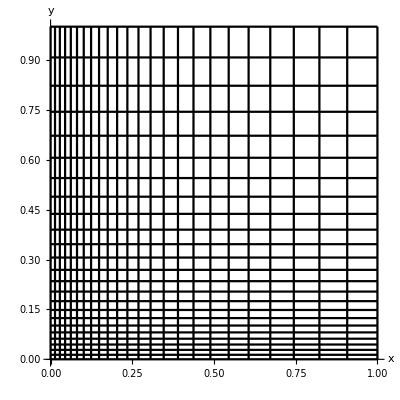

```mathematica
J = 25;
Ny=25;
xfunc[j_]:=(E^(2(j-1)/(J-1))-1)/(E^2-1);
(*xbar[j_]:=(j-1)/(J-1);*)
xbar[x_]:=1/2 Log[x*(E^2-1)+1]
yfunc[i_]:=(E^(2(i-1)/(Ny-1))-1)/(E^2-1);
(*ybar[i_] = (i-1)/(Ny-1);*)
ybar[y_]:=1/2 Log[y*(E^2-1)+1]

ContourPlot[{Evaluate[Table[x==xfunc[j],{j,1,J}]],Evaluate[Table[y==yfunc[i],{i,1,Ny}]]},{x,-0.0001,1.0001},{y,-0.0001,1.0001},Axes->True,Frame->False,ContourStyle->Directive[{Black}],AxesLabel->{"x","y"}]
```

```mathematica
Table[x==(E^(2(j-1)/(J-1))-1)/(E^2-1),{j,1,J}]//N
```

{x==0.,x==0.0389492,x==0.087591,x==0.148337,x==0.2242,x==0.318941,x==0.437258,x==0.585019,x==0.769549,x==1.}

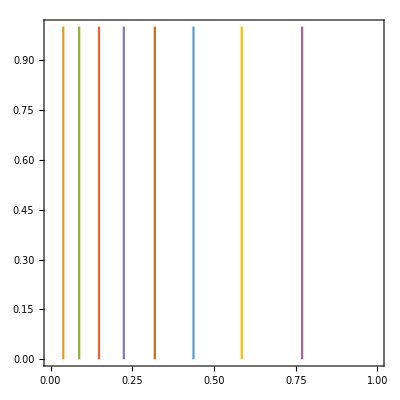

```mathematica
ContourPlot[{x==0.,x==0.03894923837706363,x==0.08759095067273646,x==0.1483370980594927,x==0.22419985551965269,x==0.3189409743731225,x==0.4372583135012321,x==0.5850187886546604,x==0.7695492909331704,x==1.},{x,0,1},{y,0,1}]
```

```mathematica
y[ybar_]:=(E^(2ybar)-1)/(E^2-1);
x[xbar_]:=(E^(2xbar)-1)/(E^2-1);
ybar[y_]:=1/2 Log[y(E^2-1)+1];
xbar[x_]:=1/2 Log[x(E^2-1)+1];
```

```mathematica
(ybar'[y[yb]])^2
```

1/4 ⅇ^(-4 yb) (-1+ⅇ^2)^2

```mathematica
ybar''[y[yb]]
```

-1/2 ⅇ^(-4 yb) (-1+ⅇ^2)^2